```mathematica
Quit[];
```

### Deriving the vev

These are the parameter redefinitions that must be made to properly normalize the meson kinetic term and give the mesons their proper masses:

```mathematica
tildeSubs={fpiT2->fpi^2/(1+(4gG)/9 vs/v),b0TfpiT2->b0 fpi^2/(1+(gf+2/3 gG)vs/v(*+2/27gG(9gf-2gG)vs^2/v^2*))};
```

Scalar potential:

```mathematica
Vs[s_]:=-b0TfpiT2 trM-b0TfpiT2/3(3gf+2gG)s/v trM+1/2 ms^2 s^2
```

```mathematica
(vsTemp==vs/.Solve[(D[Vs[s],s]/.s->vs)==0,vs])/.vsTemp->vs

%/.tildeSubs//Solve[#,vs]&//FullSimplify//StandardForm

Vs[vs]/.tildeSubs/.%;

%⟦1⟧>%⟦2⟧//FullSimplify[#,Assumptions->{v>0,ms>0,b0>0,fpi>0,trM>0,3gf+2gG≠0}]&
```

{vs==(b0TfpiT2 trM (3 gf+2 gG))/(3 ms^2 v)}

{{vs→-(3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)},{vs→(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)}}

√(4 b0 fpi^2 trM (3 gf+2 gG)^2+9 ms^2 v^2)>0

This demonstrates that this is the scalar’s true vev:

```mathematica
vevSub={vs->(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)};
```

Thankfully it has a well-defined limit when the denominator vanishes:

```mathematica
Limit[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms),gf->-2/3gG,Assumptions->{ms>0,v>0}]
```

0

```mathematica
Series[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms),{ms,∞,4}]//FullSimplify[#,Assumptions->{v>0}]&
```

(b0 fpi^2 trM (3 gf+2 gG))/(3 ms^2 v)-(b0^2 fpi^4 trM^2 (3 gf+2 gG)^3)/(27 ms^4 v^3)+O((1/ms)^5)

```mathematica
FortranForm[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)]
```

(-3*ms*v + Sqrt(4*b0*fpi**2*(3*gf + 2*gG)**2*trM + 9*ms**2*v**2))/
     -  (6*gf*ms + 4*gG*ms)

### Plotting the vev

```mathematica
subs={trM->2.3+4.8+95.,muq->2.3,mdq->4.8,msq->95.,v->246.*^3,b0->135.^2/(2.3+4.8),fpi->92.2};
```

```mathematica
Solve[Λ==vs/.vevSub/.{gf->1,gG->1},ms]//FullSimplify
%/.subs/.Λ->1000
```

{{ms→-(√5 √b0 fpi √trM)/(√(Λ (5 Λ+3 v)))},{ms→(√5 √b0 fpi √trM)/(√(Λ (5 Λ+3 v)))}}

{{ms→-3.87203},{ms→3.87203}}

```mathematica
vevSub/.{gf->1,gG->1,ms->10}/.subs
```

{vs→150.788}

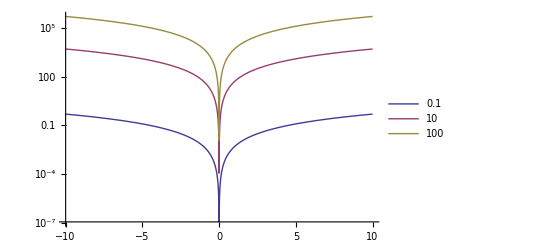

```mathematica
LogPlot[{
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->0.1}/.subs,
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->10}/.subs,
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->100}/.subs
},{s,-10,10},PlotLegends->{0.1, 10, 100}]
```

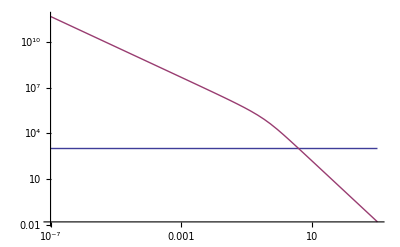

```mathematica
LogLogPlot[{1000,vs/.vevSub/.{gf->1,gG->1,ms->ms}/.subs},{ms,10^-7,1000}]
```

```mathematica
Table[{gf,gG,vs/.vevSub/.{gf->gf,gG->gG,ms->100}/.subs}//N,{gf,10^Range[-7,0,1]},{gG,10^Range[-7,0,1]}];

ListPlot3D[Flatten[%,1],AxesLabel->{"g_f","g_G","v_S (MeV)"},PlotLabel->{"m_S=1 MeV"}]
```

({1.×10^-7,1.×10^-7,0.} | {1.×10^-7,1.×10^-6,0.} | {1.×10^-7,0.00001,7.34047×10^-6} | {1.×10^-7,0.0001,0.0000606313} | {1.×10^-7,0.001,0.000603853} | {1.×10^-7,0.01,0.00603777} | {1.×10^-7,0.1,0.0603769} | {1.×10^-7,1.,0.603768}
{1.×10^-6,1.×10^-7,0.} | {1.×10^-6,1.×10^-6,0.} | {1.×10^-6,0.00001,6.47877×10^-6} | {1.×10^-6,0.0001,0.000061293} | {1.×10^-6,0.001,0.000604676} | {1.×10^-6,0.01,0.00603859} | {1.×10^-6,0.1,0.0603777} | {1.×10^-6,1.,0.603768}
{0.00001,1.×10^-7,9.86832×10^-6} | {0.00001,1.×10^-6,9.31323×10^-6} | {0.00001,0.00001,0.0000149012} | {0.00001,0.0001,0.0000693228} | {0.00001,0.001,0.000612819} | {0.00001,0.01,0.00604674} | {0.00001,0.1,0.0603859} | {0.00001,1.,0.603777}
{0.0001,1.×10^-7,0.0000905883} | {0.0001,1.×10^-6,0.0000912819} | {0.0001,0.00001,0.0000966247} | {0.0001,0.0001,0.000150949} | {0.0001,0.001,0.000694329} | {0.0001,0.01,0.00612825} | {0.0001,0.1,0.0604674} | {0.0001,1.,0.603858}
{0.001,1.×10^-7,0.000905707} | {0.001,1.×10^-6,0.000906256} | {0.001,0.00001,0.000911685} | {0.001,0.0001,0.000966038} | {0.001,0.001,0.00150943} | {0.001,0.01,0.00694334} | {0.001,0.1,0.0612825} | {0.001,1.,0.604673}
{0.01,1.×10^-7,0.00905659} | {0.01,1.×10^-6,0.00905713} | {0.01,0.00001,0.00906256} | {0.01,0.0001,0.0091169} | {0.01,0.001,0.00966029} | {0.01,0.01,0.0150942} | {0.01,0.1,0.0694334} | {0.01,1.,0.612824}
{0.1,1.×10^-7,0.0905653} | {0.1,1.×10^-6,0.0905659} | {0.1,0.00001,0.0905713} | {0.1,0.0001,0.0906256} | {0.1,0.001,0.091169} | {0.1,0.01,0.0966029} | {0.1,0.1,0.150942} | {0.1,1.,0.694332}
{1.,1.×10^-7,0.905649} | {1.,1.×10^-6,0.90565} | {1.,0.00001,0.905655} | {1.,0.0001,0.90571} | {1.,0.001,0.906253} | {1.,0.01,0.911687} | {1.,0.1,0.966025} | {1.,1.,1.50941})

-Graphics3D-

```mathematica
Solve[√(ms^2+p^2)+√(mπ^2+p^2)==mk,p]//FullSimplify
%/.ms->mk-mπ//FullSimplify
```

{{p→-(√((mk-mπ-ms) (mk-mπ+ms) (mk+mπ-ms) (mk+mπ+ms)))/(2 mk)},{p→(√((mk-mπ-ms) (mk-mπ+ms) (mk+mπ-ms) (mk+mπ+ms)))/(2 mk)}}

{{p→0},{p→0}}

```mathematica
√((aa-bb-cc)^2-4 bb cc)/.{aa->493.^2,bb->139.^2,cc->353.^2}
```

13938.9

## Adam’s new stuff

### Constants

```mathematica
condensateVals={evGG->4 π^2 0.012*10^12/gs^2,evqbarq->(-240)^3};
constants={v->246*^3,mu->2.3,md->4.8,mstr->95.};
couplings={gsGG->1,gsff->0.0001,Lam->v,ms->50}/.constants;
chiptSubs={fpi->93.,b0->137^2/(mu+md),trM->(mu+md+mstr)}/.constants;
```

### Vev from chiral Lagrangian

The Lagrangian containing the Meson kinetic terms, mass terms and interactions with S.

```mathematica
LagChiPT=(fpiT^2/4)mesKIN+(b0T fpiT^2)/2 mesMASS+(fpiT^2 gsGG)/3(S/v)mesKIN+(b0T fpiT^2)/2(gsff+2gsGG)(S/v)mesMASS+(b0T fpiT^2)/3(3gsff-2gsGG)gsGG(S^2/v^2)mesMASS;
```

Make new replacements for gsGG

```mathematica
LagChiPT2=LagChiPT//ReplaceAll[#,gsGG->gsGG*v/(3Lam)]&//FullSimplify;
```

Make sure the coefficient of S^2 in the potential is equal to 1/2 m_S^2 S^2. Define the scalar potential in terms of v_S. This is done by setting Σ=Σ^†=𝟙 and S=0. The quark masses also need to be redefined to give the physical ones in the Lagrangian above the confinement scale. Discarding the constant term, resulting potential is:

```mathematica
-(LagChiPT2-S^2 Coefficient[LagChiPT2,S,2])+1/2 ms^2 S^2;
%//ReplaceAll[#,{mesMASS-> 2*trM/(1+gsff vs/v),mesKIN-> 0}]&//Series[#,{S,0,2}]&//FullSimplify//Normal;
potChiPT1=% - (%/.S->0);
```

Minimize the potential with respect to S:

```mathematica
vsSolChiPT1=Solve[(D[potChiPT1,S]/.S->vs)==0,vs]⟦1,1,2⟧;
```

Determine the values of fpiT and b0T (in terms of vs, fpi and b0) that give the correct normalizations for the meson mass and kinetic terms.

```mathematica
LagChiPT3=LagChiPT2/.{S->vs+S};
```

```mathematica
fpiTsol=Solve[fpi^2/4==(LagChiPT3/.S-> 0//Coefficient[#,mesKIN]&),fpiT]⟦2,1,2⟧//FullSimplify;
```

```mathematica
Solve[(b0 fpi^2)/2==(LagChiPT3/.S-> 0//Coefficient[#,mesMASS]&),b0T]⟦1,1,2⟧;
b0Tsol=%/.fpiT-> fpiTsol//FullSimplify;
```

Substitute these into the above expression for vs. This gives an implicit equation for vs. Expand this to leading order in vs and solve to find the vev in terms of physical parameters.

```mathematica
vsSolChiPT1/.{b0T-> b0Tsol,fpiT-> fpiTsol};
%//Series[#,{vs,0,1}]&//Normal;

vsSubsChiPT=Solve[vs==%,vs]//FullSimplify
```

### Vev from QCD Lagrangian

Lagrangian

```mathematica
LagQCD1=-(1+gsff S/v)(mu ubaru+md dbard+mstr sbars)-1/4(1-(gs^2 gsGG)/(4 π^2 Λ)S)GG-1/2 ms^2 S^2;
```

Find S’s vev by minimizing the scalar potential

```mathematica
Solve[(D[LagQCD1,S]/.{S->vs,ubaru->evqbarq,dbard->evqbarq,sbars->evqbarq,GG->evGG})==0,vs]//FullSimplify
```

{{vs→((GG gs^2 gsGG)/(π^2 Λ)-(16 gsff (dbard md+mstr sbars+mu ubaru))/v)/(16 ms^2)}}

Scalar potential in QCD

```mathematica
potQCD=gsff S(mu+md+mstr)/v evqbarq-gs^2/(16 π^2 Lam)gsGG S evGG+1/2 ms^2 S^2;
```

Solve for the vev

```mathematica
vsSolQCD1=Solve[(D[potQCD,S]/.S->vs)==0,vs]⟦1,1,2⟧//FullSimplify
```

((evGG gs^2 gsGG)/(π^2 Lam)-(16 evqbarq gsff (md+mstr+mu))/v)/(16 ms^2)

Shift masses to give physical values

```mathematica
vsSolQCD2=vsSolQCD1/.{mu->mu/P,md->md/P,mstr->mstr/P}/.P->1+gsff vs/v//FullSimplify;
```

Expand to leading order in vs and solve the implicit equation

```mathematica
vsSolQCD2//Series[#,{vs,0,1}]&//FullSimplify//Normal;
vsSolQCD3=Solve[vs==%,vs]//FullSimplify
```

{{vs→(v (16 π^2 evqbarq gsff Lam (md+mstr+mu)-evGG gs^2 gsGG v))/(16 π^2 Lam (evqbarq gsff^2 (md+mstr+mu)-ms^2 v^2))}}

### Test a benchmark point

```mathematica
vsSubsChiPT⟦1,1,2⟧//FullSimplify
```

(3 Lam v (3 v (√(Lam ms^2 (4 b0 fpi^2 gsff trM (3 gsff Lam+2 gsGG v)+3 Lam ms^2 v^2))+√3 Lam ms^2 v)+4 √3 b0 fpi^2 gsff trM (3 gsff Lam+2 gsGG v)))/(2 gsff (√3 b0 fpi^2 trM (3 gsff Lam+2 gsGG v)^2-9 Lam v √(Lam ms^2 (4 b0 fpi^2 gsff trM (3 gsff Lam+2 gsGG v)+3 Lam ms^2 v^2))))

```mathematica
vsSolQCD3⟦1,1,2⟧/.{mstr->trM-mu-md}//FullSimplify (*/.evqbarq->-(fpi^2 mpi^2)/(2(mu+md))/.mpi->b0(mu+md)*)
```

(v (16 π^2 evqbarq gsff Lam trM-evGG gs^2 gsGG v))/(16 π^2 Lam (evqbarq gsff^2 trM-ms^2 v^2))

```mathematica
vsSubsChiPT/.chiptSubs/.couplings/.constants
vsSolQCD3/.couplings/.condensateVals/.constants
```

{{vs→-2.46002×10^9}}

{{vs→4.87828}}

#### Old result

```mathematica
oldSol=(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms);
```